# Mathematica — это круто!

## Интерфейс

Назовём областью редактирования в окне Вольфрам Математики то белое поле с текстом, на котором, в частности, написана эта инструкция.
Область редактирования состоит из ячеек. Обратите внимание на бледные скобочки типа «]» в правой части области редактирования (слева от полосы прокрутки) — они показывают размеры ячеек по вертикали. Но в ячейке НЕ могут лежать другие ячейки.
«Ячейки», в которых лежат ячейки, на самом деле являются группами ячеек. Группа ячеек может быть свёрнута двойным нажатием на скобку этой группы. Попробуйте!  В данном окне также предусмотрена возможность сворачивать и разворачивать группы по нажатию на синие стрелочки слева от заголовка группы.

Чтобы стало понятнее, можно включить (и выключить, если не понравится) выделение собственно ячеек (не групп):

```mathematica
DynamicModule[{
text=<|
True->"Включить выделение ячеек",
False->"Выключить выделение ячеек"
|>,
frameQ=True
},

Dynamic[
Button[text@frameQ,
SetOptions[FrontEnd`EvaluationNotebook[],CellFrame->frameQ];
frameQ=!frameQ;
],
TrackedSymbols:>{frameQ}
]
]
```

Каждая ячейка характеризуется множеством свойств. Мы сейчас остановимся только на одном — Evaluatable. Назовём ячейки, у которых это свойство имеет значение True, вычислимыми, а те, у которых значение этого свойства False — текстовыми. Вычислимые ячейки и есть то, ради чего мы собрались. В них можно считать интегралы, формировать таблицы и вообще делать всё, что душе угодно. Текстовые (например, эта) нужны для больших комментариев, описаний и заголовков. Далее будем называть вычислимые ячейки просто ячейками, если не сказано иное.

```mathematica
2+2
```

4

Документация

Если вы встретили непонятный значок или слово, то вы можете узнать его смысл, поставив клавиатурный курсор в непонятное выражение или сразу после него и нажав на клавиатуре F1. Также комбинацию символов можно выделять.

Нажатие клавиши F1 приводит к открытию окна документации (справки) по WM. Общее меню документации вызывается через меню Help → Wolfram Documentation. Это неисчерпаемый и основной источник знаний по WM.

```mathematica
Integrate[x,{x,1,2}]
```

3/2

Алгоритм вычисления ячейки

Устанавливаете клавиатурный курсор (мигающую палочку в буковках) в любое место любой строки выбранной вами ячейки.

Нажимаете Shift+Enter.

Дожидаетесь конца вычислений. На время вычислений ячейки её скобка становится чёрной и жирной.

К слову, многие вычисления в этом файле будут занимать доли секунды, поэтому вы можете не заметить изменение вида скобки вычисляемой ячейки.

Результат вычислений помещается в ячейку вывода, которая формируется сразу после вычисленной ячейки. Упражнение: Вычислите ячейки ниже.

```mathematica
2+2
```

```mathematica
∫_0^∞ Sin[x]/x ⅆx
```

π/2

## Крутые примеры

Графики

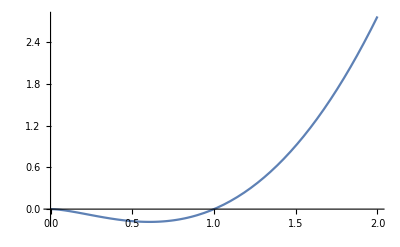

```mathematica
Plot[x^2 Log@x,{x,0,2}]
```

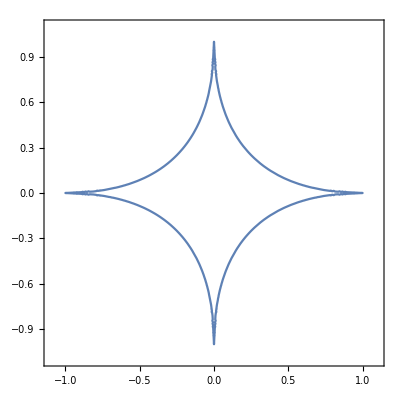

```mathematica
ContourPlot[Abs[x]^0.5+Abs[y]^0.5==1,{x,-1.1,1.1},{y,-1.1,1.1}]
```

```mathematica
Manipulate[
ContourPlot[Abs[x]^α+Abs[y]^α==1,{x,-1.1,1.1},{y,-1.1,1.1}],
{α,0.1,3}
]
```

А теперь построим несколько аналогичных графиков для разных степеней, и распараллелим заодно:

```mathematica
Log@x
```

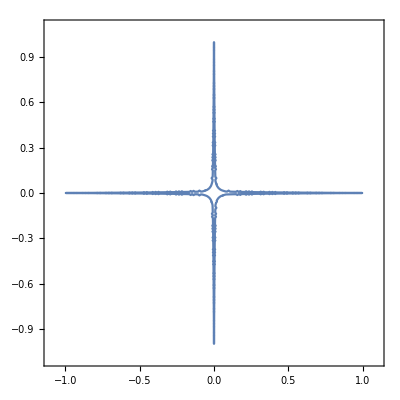
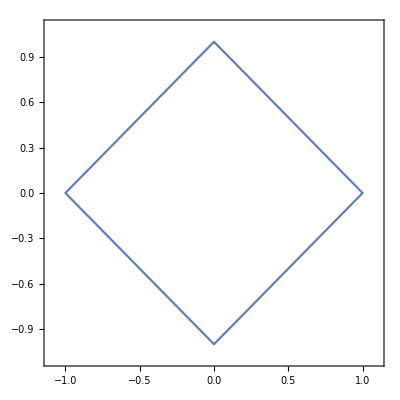
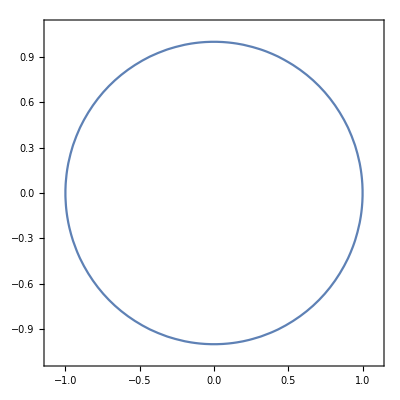
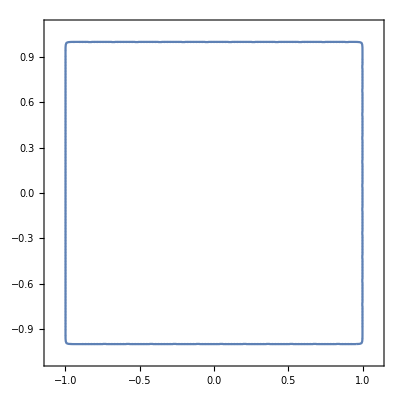

```mathematica
ContourPlot[Abs[x]^#+Abs[y]^#==1,{x,-1.1,1.1},{y,-1.1,1.1}]&/@{0.2,1,2,100}//Parallelize
```

Линейные уравнения

```mathematica
sol=Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
FunctionDomain[x/.sol,{a,b,c}]
```

a≠0&&-b^2+4 a c≤0

Упрощение сложных выражений

```mathematica
Sin[x]^2+Cos[x]^2
```

Cos[x]^2+Sin[x]^2

```mathematica
FullSimplify[Sin[x]^2+Cos[x]^2]
Simplify[Sin[x]^2+Cos[x]^2]
```

1

1

```mathematica
expr=Gamma[x]/Gamma[x+1]
```

Gamma[x]/Gamma[1+x]

```mathematica
Simplify@expr
```

Gamma[x]/Gamma[1+x]

```mathematica
FullSimplify@expr
```

1/x

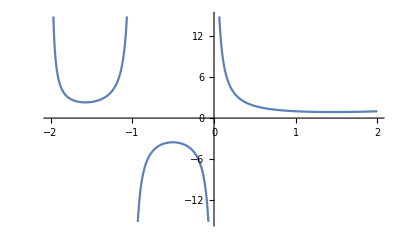

```mathematica
Plot[Gamma@x,{x,-2,2}]
```

```mathematica
x+x
```

2 x

Дифференцирование

```mathematica
D[Log@x x^2,x]
```

x+2 x Log[x]

```mathematica
f[x_]:=Log@x x^2
```

```mathematica
FullSimplify[f''''[y^2],y>0]
```

-2/y^4

```mathematica
f''''
```

-2/#1^2&

```mathematica
g[x_,y_]:=x Log@y
```

```mathematica
g'[x,y]
```

g'[x,y]

```mathematica
SetDelayed
D
```

Дифференциальные уравнения

```mathematica
a==b
a===b
```

a==b

False

```mathematica
a=2;
b=2;
a===b
```

True

```mathematica
2===2
```

True

```mathematica
DSolve[y''[t]==-g,y[t],t]
```

{{y[t]→-(g t^2)/2+C[1]+t C[2]}}

```mathematica
DSolve[{
y''[t]==-g,
y'[0]==0,
y[0]==10
},y[t],t]
DSolve[
y''[t]==-g&&
y'[0]==0&&
y[0]==10
,y[t],t]
```

{{y[t]→1/2 (20-g t^2)}}

{{y[t]→1/2 (20-g t^2)}}

Интегралы

```mathematica
Integrate[ⅇ^(α x),{x,0,∞},Assumptions->α<0]
```

-1/α

```mathematica
Assuming[α<0,∫_0^∞ ⅇ^(α x)ⅆx]
```

-1/α

# Основные принципы

## Принципы работы ядра

Ядро

Ядро — это вычислительный аппарат языка Wolfram. Что такое вычисление и каким образом ядро их производит, будет подробнее раскрыто далее.

Структура выражений

## Элементарные выражения

Элементарные выражения бывают нескольких видов:

символы — последовательность букв, цифр и некоторых спецсимволов, которая не может начинаться с цифры (x, f, t0, Lf90, πfk90p)

строки — любая последовательность символов (не в понимании предыдущего пункта, а в обыденном понимании, т.е. буквы, цифры, пробелы, спецсимволы и пр.; экранирующий символ “\” имеет тот же смысл, как и в других языках программирования), заключённая в кавычки “” (пример: “anything you want...”)

```mathematica
"dsklfjdsklfj \\n"
```

dsklfjdsklfj \n

```mathematica
"dsklfjdsklfj \n"
```

dsklfjdsklfj

```mathematica
str="dfjsdkfl";
"∫_6^444 xⅆx"<>str
```

∫_6^444 xⅆxdfjsdkfl

```mathematica
Head@ToString[2]
```

2

```mathematica
"2"==2
```

False

```mathematica
Nest[#+1.*^-14&,1,1*^10]
```

1.0001

```mathematica
Compile[{},
Module[{x=1.,i},
For[i=1,i<1.*^10,i++,
x+=1.*^-14
];
x
]
][]
```

1.0001

целые числа (могут быть оооочень большими: 0, 1, -5, 516514198515498498465)

десятичные дроби (0., 1., -8.09, 4.54655×10^20 (записывается как 4.54655*^20))

## Сложные выражения

Любые выражения могут быть либо элементарными, либо состоять из элементарных (сложные). Сложные выражения состоят из последовательности выражений (элементарных или сложных), нулевое из которых называется головой выражения, а остальные — первым, вторым и т.д. аргументами. Аргументов у сложного выражения может совсем не быть.

Примеры сложных выражений:

```mathematica
f[x,g[t]]
```

```mathematica
f[]
f
```

```mathematica
g[t][f[y]]
g[t,f[y]]
```

```mathematica
g[t][f[y]]//Head
```

g[t]

Неформально также можно сказать, что выражение с какой-нибудь головой f и аргументами x1, x2 и т.д. — это применение функции/головы/символа f к соответствующим аргументам. То есть, в данном контексте понятия «функция f», «голова f» и «символ f» тождественны.

## Головы элементарных выражений

У элементарных выражений, как и у сложных, есть голова. В некотором смысле, голова элементарного выражения — это тип данных.

символы — Symbol

```mathematica
Head@f
```

Symbol

Упражнение: может ли у сложного выражения быть голова Symbol?

```mathematica
Symbol["x"]
```

строки — String

целые числа — Integer

десятичные дроби — Real

## Нахождение головы выражения

Символ Head, применённый к выражению, выдаёт его голову. Но не стоит забывать про общий порядок вычислений: сначала вычисляется аргумент функции Head, а затем обрабатывается применение Head к этому аргументу. Примеры:

Упражнение: применить Head 1, 2, 3, 4 и 5 раз к следующему выражению и понять, почему получается такой результат:

```mathematica
f[][2+2][g[x]]
```

Сложно: использовать для этого функцию NestList.